```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
h5data=Import["tst.hdf5"]
```

{/root/data_0,/root/data_1,/root/data_2}

```mathematica
h5data=Import["tst.hdf5","Attributes"]
```

{/root→{EC→1.2,EJ→30.02,_eigenvals_stored→[-21.84390814  -6.17107609   7.93584546  20.84011423  28.10771803],_sys_type→Cooper pair box,ncut→31,ng→0.3},/root/data_0→{data_info_0→ng},/root/data_1→{data_info_1→spectrum energies},/root/data_2→{data_info_2→states}}

```mathematica
ngdata=Import["tst.hdf5",{"Datasets","/root/data_0"}]
```

{-2.,-1.98174,-1.96347,-1.94521,-1.92694,-1.90868,-1.89041,-1.87215,-1.85388,-1.83562,-1.81735,-1.79909,-1.78082,-1.76256,-1.74429,-1.72603,-1.70776,-1.6895,-1.67123,-1.65297,-1.6347,-1.61644,-1.59817,-1.57991,-1.56164,-1.54338,-1.52511,-1.50685,-1.48858,-1.47032,-1.45205,-1.43379,-1.41553,-1.39726,-1.379,-1.36073,-1.34247,-1.3242,-1.30594,-1.28767,-1.26941,-1.25114,-1.23288,-1.21461,-1.19635,-1.17808,-1.15982,-1.14155,-1.12329,-1.10502,-1.08676,-1.06849,-1.05023,-1.03196,-1.0137,-0.995434,-0.977169,-0.958904,-0.940639,-0.922374,-0.90411,-0.885845,-0.86758,-0.849315,-0.83105,-0.812785,-0.794521,-0.776256,-0.757991,-0.739726,-0.721461,-0.703196,-0.684932,-0.666667,-0.648402,-0.630137,-0.611872,-0.593607,-0.575342,-0.557078,-0.538813,-0.520548,-0.502283,-0.484018,-0.465753,-0.447489,-0.429224,-0.410959,-0.392694,-0.374429,-0.356164,-0.3379,-0.319635,-0.30137,-0.283105,-0.26484,-0.246575,-0.228311,-0.210046,-0.191781,-0.173516,-0.155251,-0.136986,-0.118721,-0.100457,-0.0821918,-0.0639269,-0.0456621,-0.0273973,-0.00913242,0.00913242,0.0273973,0.0456621,0.0639269,0.0821918,0.100457,0.118721,0.136986,0.155251,0.173516,0.191781,0.210046,0.228311,0.246575,0.26484,0.283105,0.30137,0.319635,0.3379,0.356164,0.374429,0.392694,0.410959,0.429224,0.447489,0.465753,0.484018,0.502283,0.520548,0.538813,0.557078,0.575342,0.593607,0.611872,0.630137,0.648402,0.666667,0.684932,0.703196,0.721461,0.739726,0.757991,0.776256,0.794521,0.812785,0.83105,0.849315,0.86758,0.885845,0.90411,0.922374,0.940639,0.958904,0.977169,0.995434,1.0137,1.03196,1.05023,1.06849,1.08676,1.10502,1.12329,1.14155,1.15982,1.17808,1.19635,1.21461,1.23288,1.25114,1.26941,1.28767,1.30594,1.3242,1.34247,1.36073,1.379,1.39726,1.41553,1.43379,1.45205,1.47032,1.48858,1.50685,1.52511,1.54338,1.56164,1.57991,1.59817,1.61644,1.6347,1.65297,1.67123,1.6895,1.70776,1.72603,1.74429,1.76256,1.78082,1.79909,1.81735,1.83562,1.85388,1.87215,1.89041,1.90868,1.92694,1.94521,1.96347,1.98174,2.}

```mathematica
energiesdata=Import["tst.hdf5",{"Datasets","/root/data_1"}]
```

{{-21.8439,-6.17108,7.93585,20.8401},{-21.8439,-6.1711,7.93623,20.8355},{-21.8439,-6.17116,7.93738,20.8216},{-21.8439,-6.17126,7.93928,20.7989},{-21.8439,-6.1714,7.94191,20.7679},{-21.8439,-6.17158,7.94524,20.7292},{-21.8439,-6.17179,7.94922,20.6839},{-21.8439,-6.17204,7.9538,20.6327},{-21.8439,-6.17231,7.95894,20.5767},{-21.8439,-6.17261,7.96455,20.517},{-21.8439,-6.17293,7.97058,20.4545},{-21.8439,-6.17326,7.97695,20.3903},{-21.8439,-6.17361,7.98357,20.3252},{-21.8438,-6.17397,7.99036,20.2602},{-21.8438,-6.17433,7.99723,20.1961},{-21.8438,-6.17469,8.00409,20.1337},{-21.8438,-6.17504,8.01085,20.0736},{-21.8438,-6.17538,8.01742,20.0165},{-21.8438,-6.17571,8.02371,19.963},{-21.8438,-6.17601,8.02964,19.9136},{-21.8438,-6.17629,8.03512,19.8686},{-21.8438,-6.17655,8.04008,19.8285},{-21.8438,-6.17677,8.04446,19.7937},{-21.8438,-6.17696,8.04818,19.7644},{-21.8438,-6.17712,8.0512,19.7408},{-21.8438,-6.17724,8.05348,19.7232},{-21.8438,-6.17731,8.05499,19.7116},{-21.8438,-6.17735,8.05569,19.7062},{-21.8438,-6.17734,8.05559,19.707},{-21.8438,-6.1773,8.05468,19.7139},{-21.8438,-6.17721,8.05299,19.727},{-21.8438,-6.17708,8.05052,19.7462},{-21.8438,-6.17692,8.04731,19.7712},{-21.8438,-6.17672,8.04342,19.8019},{-21.8438,-6.17649,8.03889,19.8381},{-21.8438,-6.17623,8.03379,19.8794},{-21.8438,-6.17594,8.02819,19.9255},{-21.8438,-6.17563,8.02217,19.976},{-21.8438,-6.1753,8.0158,20.0305},{-21.8438,-6.17495,8.00917,20.0884},{-21.8438,-6.1746,8.00238,20.1491},{-21.8438,-6.17424,7.99551,20.212},{-21.8438,-6.17388,7.98865,20.2764},{-21.8439,-6.17352,7.98189,20.3415},{-21.8439,-6.17318,7.97533,20.4064},{-21.8439,-6.17285,7.96904,20.4703},{-21.8439,-6.17253,7.96311,20.5322},{-21.8439,-6.17224,7.95761,20.5911},{-21.8439,-6.17197,7.9526,20.646},{-21.8439,-6.17174,7.94816,20.6958},{-21.8439,-6.17153,7.94434,20.7396},{-21.8439,-6.17136,7.94119,20.7764},{-21.8439,-6.17123,7.93874,20.8054},{-21.8439,-6.17114,7.93702,20.8259},{-21.8439,-6.17109,7.93606,20.8375},{-21.8439,-6.17108,7.93587,20.8398},{-21.8439,-6.17111,7.93645,20.8328},{-21.8439,-6.17118,7.93779,20.8167},{-21.8439,-6.17129,7.93987,20.7919},{-21.8439,-6.17144,7.94268,20.7589},{-21.8439,-6.17163,7.94617,20.7185},{-21.8439,-6.17185,7.95031,20.6716},{-21.8439,-6.1721,7.95504,20.6191},{-21.8439,-6.17238,7.9603,20.5621},{-21.8439,-6.17269,7.96602,20.5016},{-21.8439,-6.17301,7.97215,20.4386},{-21.8439,-6.17335,7.97858,20.374},{-21.8439,-6.1737,7.98525,20.3089},{-21.8438,-6.17406,7.99207,20.2441},{-21.8438,-6.17442,7.99895,20.1803},{-21.8438,-6.17478,8.00579,20.1184},{-21.8438,-6.17513,8.01251,20.0591},{-21.8438,-6.17546,8.01902,20.0028},{-21.8438,-6.17578,8.02523,19.9503},{-21.8438,-6.17609,8.03105,19.9019},{-21.8438,-6.17636,8.03641,19.8581},{-21.8438,-6.17661,8.04123,19.8193},{-21.8438,-6.17683,8.04545,19.7858},{-21.8438,-6.17701,8.049,19.7579},{-21.8438,-6.17715,8.05184,19.7358},{-21.8438,-6.17726,8.05393,19.7197},{-21.8438,-6.17733,8.05524,19.7097},{-21.8438,-6.17735,8.05574,19.7058},{-21.8438,-6.17734,8.05544,19.7081},{-21.8438,-6.17728,8.05433,19.7166},{-21.8438,-6.17718,8.05244,19.7312},{-21.8438,-6.17705,8.04978,19.7519},{-21.8438,-6.17687,8.0464,19.7783},{-21.8438,-6.17667,8.04235,19.8104},{-21.8438,-6.17643,8.03767,19.8479},{-21.8438,-6.17616,8.03244,19.8905},{-21.8438,-6.17586,8.02672,19.9378},{-21.8438,-6.17555,8.0206,19.9893},{-21.8438,-6.17521,8.01416,20.0447},{-21.8438,-6.17486,8.00748,20.1033},{-21.8438,-6.17451,8.00066,20.1647},{-21.8438,-6.17415,7.99379,20.228},{-21.8438,-6.17379,7.98695,20.2927},{-21.8439,-6.17344,7.98023,20.3578},{-21.8439,-6.17309,7.97373,20.4226},{-21.8439,-6.17277,7.96752,20.486},{-21.8439,-6.17246,7.96169,20.5473},{-21.8439,-6.17217,7.95631,20.6053},{-21.8439,-6.17191,7.95144,20.6589},{-21.8439,-6.17168,7.94715,20.7073},{-21.8439,-6.17149,7.94349,20.7494},{-21.8439,-6.17133,7.94051,20.7844},{-21.8439,-6.1712,7.93824,20.8113},{-21.8439,-6.17112,7.93671,20.8297},{-21.8439,-6.17108,7.93594,20.8389},{-21.8439,-6.17108,7.93594,20.8389},{-21.8439,-6.17112,7.93671,20.8297},{-21.8439,-6.1712,7.93824,20.8113},{-21.8439,-6.17133,7.94051,20.7844},{-21.8439,-6.17149,7.94349,20.7494},{-21.8439,-6.17168,7.94715,20.7073},{-21.8439,-6.17191,7.95144,20.6589},{-21.8439,-6.17217,7.95631,20.6053},{-21.8439,-6.17246,7.96169,20.5473},{-21.8439,-6.17277,7.96752,20.486},{-21.8439,-6.17309,7.97373,20.4226},{-21.8439,-6.17344,7.98023,20.3578},{-21.8438,-6.17379,7.98695,20.2927},{-21.8438,-6.17415,7.99379,20.228},{-21.8438,-6.17451,8.00066,20.1647},{-21.8438,-6.17486,8.00748,20.1033},{-21.8438,-6.17521,8.01416,20.0447},{-21.8438,-6.17555,8.0206,19.9893},{-21.8438,-6.17586,8.02672,19.9378},{-21.8438,-6.17616,8.03244,19.8905},{-21.8438,-6.17643,8.03767,19.8479},{-21.8438,-6.17667,8.04235,19.8104},{-21.8438,-6.17687,8.0464,19.7783},{-21.8438,-6.17705,8.04978,19.7519},{-21.8438,-6.17718,8.05244,19.7312},{-21.8438,-6.17728,8.05433,19.7166},{-21.8438,-6.17734,8.05544,19.7081},{-21.8438,-6.17735,8.05574,19.7058},{-21.8438,-6.17733,8.05524,19.7097},{-21.8438,-6.17726,8.05393,19.7197},{-21.8438,-6.17715,8.05184,19.7358},{-21.8438,-6.17701,8.049,19.7579},{-21.8438,-6.17683,8.04545,19.7858},{-21.8438,-6.17661,8.04123,19.8193},{-21.8438,-6.17636,8.03641,19.8581},{-21.8438,-6.17609,8.03105,19.9019},{-21.8438,-6.17578,8.02523,19.9503},{-21.8438,-6.17546,8.01902,20.0028},{-21.8438,-6.17513,8.01251,20.0591},{-21.8438,-6.17478,8.00579,20.1184},{-21.8438,-6.17442,7.99895,20.1803},{-21.8438,-6.17406,7.99207,20.2441},{-21.8439,-6.1737,7.98525,20.3089},{-21.8439,-6.17335,7.97858,20.374},{-21.8439,-6.17301,7.97215,20.4386},{-21.8439,-6.17269,7.96602,20.5016},{-21.8439,-6.17238,7.9603,20.5621},{-21.8439,-6.1721,7.95504,20.6191},{-21.8439,-6.17185,7.95031,20.6716},{-21.8439,-6.17163,7.94617,20.7185},{-21.8439,-6.17144,7.94268,20.7589},{-21.8439,-6.17129,7.93987,20.7919},{-21.8439,-6.17118,7.93779,20.8167},{-21.8439,-6.17111,7.93645,20.8328},{-21.8439,-6.17108,7.93587,20.8398},{-21.8439,-6.17109,7.93606,20.8375},{-21.8439,-6.17114,7.93702,20.8259},{-21.8439,-6.17123,7.93874,20.8054},{-21.8439,-6.17136,7.94119,20.7764},{-21.8439,-6.17153,7.94434,20.7396},{-21.8439,-6.17174,7.94816,20.6958},{-21.8439,-6.17197,7.9526,20.646},{-21.8439,-6.17224,7.95761,20.5911},{-21.8439,-6.17253,7.96311,20.5322},{-21.8439,-6.17285,7.96904,20.4703},{-21.8439,-6.17318,7.97533,20.4064},{-21.8439,-6.17352,7.98189,20.3415},{-21.8438,-6.17388,7.98865,20.2764},{-21.8438,-6.17424,7.99551,20.212},{-21.8438,-6.1746,8.00238,20.1491},{-21.8438,-6.17495,8.00917,20.0884},{-21.8438,-6.1753,8.0158,20.0305},{-21.8438,-6.17563,8.02217,19.976},{-21.8438,-6.17594,8.02819,19.9255},{-21.8438,-6.17623,8.03379,19.8794},{-21.8438,-6.17649,8.03889,19.8381},{-21.8438,-6.17672,8.04342,19.8019},{-21.8438,-6.17692,8.04731,19.7712},{-21.8438,-6.17708,8.05052,19.7462},{-21.8438,-6.17721,8.05299,19.727},{-21.8438,-6.1773,8.05468,19.7139},{-21.8438,-6.17734,8.05559,19.707},{-21.8438,-6.17735,8.05569,19.7062},{-21.8438,-6.17731,8.05499,19.7116},{-21.8438,-6.17724,8.05348,19.7232},{-21.8438,-6.17712,8.0512,19.7408},{-21.8438,-6.17696,8.04818,19.7644},{-21.8438,-6.17677,8.04446,19.7937},{-21.8438,-6.17655,8.04008,19.8285},{-21.8438,-6.17629,8.03512,19.8686},{-21.8438,-6.17601,8.02964,19.9136},{-21.8438,-6.17571,8.02371,19.963},{-21.8438,-6.17538,8.01742,20.0165},{-21.8438,-6.17504,8.01085,20.0736},{-21.8438,-6.17469,8.00409,20.1337},{-21.8438,-6.17433,7.99723,20.1961},{-21.8438,-6.17397,7.99036,20.2602},{-21.8439,-6.17361,7.98357,20.3252},{-21.8439,-6.17326,7.97695,20.3903},{-21.8439,-6.17293,7.97058,20.4545},{-21.8439,-6.17261,7.96455,20.517},{-21.8439,-6.17231,7.95894,20.5767},{-21.8439,-6.17204,7.9538,20.6327},{-21.8439,-6.17179,7.94922,20.6839},{-21.8439,-6.17158,7.94524,20.7292},{-21.8439,-6.1714,7.94191,20.7679},{-21.8439,-6.17126,7.93928,20.7989},{-21.8439,-6.17116,7.93738,20.8216},{-21.8439,-6.1711,7.93623,20.8355},{-21.8439,-6.17108,7.93585,20.8401}}

```mathematica
plotdata=TemporalData[energiesdata, {ngdata}];
```

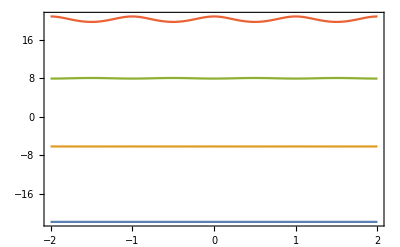

```mathematica
ListPlot[plotdata,Joined->True, Frame->True,Axes->False]
```